# An AutoML application of algebraic evaluation of binary classifiers

This notebook details an experiment in AutoML using algebraic evaluators on unlabeled data. The basic idea is that highly correlated trios would trigger failures in the evaluator that assumes error independence for them. Thus we can search for least correlated trios on unlabeled data without ever knowing the true labels on the test set. Here we want to confirm whether this happens - are the trios selected because they did not trigger evaluator failures actually less correlated than the ones that did?

## Collecting the components of the experiment

We’ll continue using the dataset common to all the notebooks here - the UCI Adult set. Let’s make sure we have the dataset and related metadata.

```mathematica
{tsvHeader, benchmarkData} = ImportPennMLBenchmarksDataset["adult"];
```

```mathematica
tsvHeader
```

{age,workclass,fnlwgt,education,education-num,marital-status,occupation,relationship,race,sex,capital-gain,capital-loss,hours-per-week,native-country,target}

Some metadata about the features that is used to manually control the feature types used by Mathematica to train classifiers.

```mathematica
uciAdultFeatures
```

{{1,Numerical},{2,Nominal},{3,Numerical},{4,Nominal},{5,Nominal},{6,Nominal},{7,Nominal},{8,Nominal},{9,Nominal},{10,Nominal},{11,Numerical},{12,Numerical},{13,Numerical},{14,Nominal}}

## Training a trio

Let’s train a trio now and evaluate it algebraically on unlabeled test data. We start by picking a disjoint feature partition to encourage our classifiers to be error independent. Our choice has the 1st two classifiers using 3 features and the last one using 4.

```mathematica
featurePartition={
{{4,"Nominal"},{5,"Nominal"},{7,"Nominal"}},{{6,"Nominal"},{8,"Nominal"},{9,"Nominal"}},{{1,"Numerical"},{3,"Numerical"},{11,"Numerical"},{12,"Numerical"}}
};
```

Let’s train classifiers on this single random train/test split. We train on 11K , test on 18K. At the end, we get the ensemble voting counts by true label.

```mathematica
searchSet=benchmarkData;
classifierTypes = Table["NaiveBayes",{3}];
classifiersFeatures=featurePartition;
trainTestSplit=Association[0->(RandomSample[searchSet[0]]//{Take[#,6000],Take[#,-400]}&),1->(RandomSample[searchSet[1]]//{Take[#,6000],Take[#,-800]}&)];
trainingIndices=Transpose@{
RandomSample[Range@6000]//Partition[#,2000]&,
RandomSample[Range@6000]//Partition[#,2000]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,trainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
voteCountsByLabel=LabelCounts[classifiers,classifiersData]
```

<|0→<|{0,1,0}→43,{0,0,0}→154,{0,0,1}→40,{1,0,0}→107,{1,0,1}→28,{1,1,1}→4,{1,1,0}→12,{0,1,1}→12|>,1→<|{1,0,0}→128,{1,1,0}→136,{1,1,1}→251,{0,1,1}→81,{0,1,0}→65,{1,0,1}→73,{0,0,0}→40,{0,0,1}→26|>|>

Let’s evaluate them algebraically and also get the actual ground truth to see how well the estimate went.

```mathematica
AlgebraicallyEvaluateClassifiers[classifiers,classifiersData]
```

{<|P_α→0.333333,P_(1,α)→0.6225,P_(2,α)→0.8225,P_(3,α)→0.79,P_(1,β)→0.735,P_(2,β)→0.66625,P_(3,β)→0.53875,Γ_(1,2,α)→-0.0270063,Γ_(1,3,α)→0.000725,Γ_(2,3,α)→0.002725,Γ_(1,2,β)→-0.00594375,Γ_(1,3,β)→0.00901875,Γ_(2,3,β)→0.0560578,Γ_(1,2,3,α)→-0.000442625,Γ_(1,2,3,β)→0.00591845|>,{{{P_α→0.308794,P_(1,α)→0.225011,P_(1,β)→0.544731,P_(2,α)→0.132911,P_(2,β)→0.340827,P_(3,α)→0.115553,P_(3,β)→0.225772},{P_α→0.691206,P_(1,α)→0.455269,P_(1,β)→0.774989,P_(2,α)→0.659173,P_(2,β)→0.867089,P_(3,α)→0.774228,P_(3,β)→0.884447}}}}

Not too shabby. But not great. We can see in the ground truth values that the error correlation of classifiers 2 and 3 is 5.8%. The prevalence estimate is off (57% versus the true 33% value) in the 2nd returned solution. But its accuracy estimates are close to the true values. Since the goal of these experiments is to find least correlated trios, we gloss over this estimation error and continue.

## Automating many train/test splits

To robustify our selected trios, we carry out multiple train/test splits and collect statistics on the certifiable failures of the algebraic evaluator. Let’s start by coding the functions that will collect those evaluator failure statistics.

```mathematica
Clear[IsEvaluatorFailureImaginaryQ]
IsEvaluatorFailureImaginaryQ[algebraicSols_List]:= (* We only need to test on one of the two solutions*)
First@algebraicSols//
(* Extracting the numerical estimates *)
Last/@#&//
(* Are any of them imaginary? *)
Head/@#&//Counts//
If[Lookup[#,Complex,0]>0,True,False]&
```

We have to be careful with how we proceed in the experiment. Our ultimate intent is to explore the possibility of Auto-ML on a large body of unlabeled data by using our algebraic evaluator.
In the operational setting we envision for the evaluator, there will be no overlap between the training data and the unlabeled data. You have some labeled data for training classifiers. Could those classifiers be selected for best ability to self-evaluate on the unlabeled data?
To get closer to this operational context, we will do a strict enforcement of train/test splits. The training
data pool and test data pool will remain separate through out our runs.

```mathematica
Map[Length,benchmarkData]
```

<|1→37155,0→11687|>

```mathematica
globalTrainTestSplit=Map[TakeDrop[RandomSample@#,7000]&,benchmarkData];
```

```mathematica
Map[Length,globalTrainTestSplit,{2}]
```

<|1→{7000,30155},0→{7000,4687}|>

```mathematica
classifierTypes = Table["NaiveBayes",{3}];
classifiersFeatures=featurePartition;
Timing[runs =Table[
runTrainTestSplit=Association[
0->({Take[globalTrainTestSplit[0]//First//RandomSample,6000],Take[globalTrainTestSplit[0]//Last//RandomSample,200]}),
1->({Take[globalTrainTestSplit[1]//First//RandomSample,6000],Take[globalTrainTestSplit[1]//Last//RandomSample,400]})];
trainingIndices=Transpose@{
(* Random selection of 0 label training data between the three classifiers *)
RandomSample[Range@6000]//Partition[#,2000]&,
(* Same random selection for the 1 label *)
RandomSample[Range@6000]//Partition[#,2000]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
AlgebraicallyEvaluateClassifiers[classifiers, classifiersData],
{20}];]
```

{39.189,Null}

```mathematica
First@runs
```

{<|P_α→0.333333,P_(1,α)→0.64,P_(2,α)→0.88,P_(3,α)→0.865,P_(1,β)→0.7325,P_(2,β)→0.6925,P_(3,β)→0.4775,Γ_(1,2,α)→-0.0082,Γ_(1,3,α)→0.0064,Γ_(2,3,α)→0.0038,Γ_(1,2,β)→-0.00225625,Γ_(1,3,β)→0.0127313,Γ_(2,3,β)→0.0443313,Γ_(1,2,3,α)→-0.008139,Γ_(1,2,3,β)→0.00757347|>,{{{P_α→0.351375,P_(1,α)→0.187388,P_(1,β)→0.497671,P_(2,α)→0.108384,P_(2,β)→0.290422,P_(3,α)→0.284495,P_(3,β)→0.172554},{P_α→0.648625,P_(1,α)→0.502329,P_(1,β)→0.812612,P_(2,α)→0.709578,P_(2,β)→0.891616,P_(3,α)→0.827446,P_(3,β)→0.715505}}}}

Were any imaginary?

```mathematica
Last/@runs//Last/@#&//IsEvaluatorFailureImaginaryQ/@#&//Counts
```

<|False→20|>

No. Let’s check now for the other possible evaluation failure - out of bound real values.

```mathematica
Clear[IsEvaluatorFailureOutOfBoundsRealQ]
IsEvaluatorFailureOutOfBoundsRealQ[sols_List]:=If[IsEvaluatorFailureImaginaryQ@sols == False,
First@sols//Last/@#&//
(
(Min@#<0) || 
(Max@#>1))&,
False]
```

```mathematica
IsEvaluatorFailureOutOfBoundsRealQ[First@runs//Last//First]
```

False

```mathematica
Last/@runs//Last/@#&//IsEvaluatorFailureOutOfBoundsRealQ/@#&//Counts
```

<|False→19,True→1|>

#### Are there any feature disjoint sets that cause evaluator failures?

So, were we just lucky or are the failures of the algebraic evaluator to hard to induce? Let’s go searching for failures.

```mathematica
classifierTypes = Table["NaiveBayes",{3}];
Timing[runs =Table[

(* The random train/test split *)
runTrainTestSplit=Association[
0->({Take[globalTrainTestSplit[0]//First//RandomSample,6000],Take[globalTrainTestSplit[0]//Last//RandomSample,200]}),
1->({Take[globalTrainTestSplit[1]//First//RandomSample,6000],Take[globalTrainTestSplit[1]//Last//RandomSample,400]})];

(* A random disjoint partition of the dataset features *)
classifiersFeatures=uciAdultFeatures//RandomSample//Partition[#,UpTo@3]&//Take[#,3]&;

(* Training and evaluatin the trio of classifiers *)
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
trainingIndices=Transpose@{
(* Random selection of 0 label training data between the three classifiers *)
RandomSample[Range@6000]//Partition[#,2000]&,
(* Same random selection for the 1 label *)
RandomSample[Range@6000]//Partition[#,2000]&};
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
AlgebraicallyEvaluateClassifiers[classifiers, classifiersData],
{100}];]
```

$Aborted

```mathematica
Last/@runs//First/@#&//IsEvaluatorFailureOutOfBoundsRealQ/@#&//Counts
Last/@runs//IsEvaluatorFailureImaginaryQ/@#&//Counts
```

<|True→27,False→73|>

<|False→100|>

Awesome! So failures do occur. Before we go on to break the evaluator further and induce imaginary number estimates, let’s take a peek at the correlations of those evaluations that returned out of bound estimates

```mathematica
failedRealBoundsEvaluations=Select[runs,IsEvaluatorFailureOutOfBoundsRealQ@First@Last@#&];
```

Let' s pick one of the two returned solutions for each of the runs. Remember, this is the decoding ambiguity that is inherent in error-correcting codes. Since it can be proven that the two returned solutions are related by a symmetry transformation of the labels, the shapes of the variation we will visualize with one choice is the mirror image of the other. We’ll check that to make is sure, but first let’s visualize one decoding choice, say, the ones with lowest prevalence.

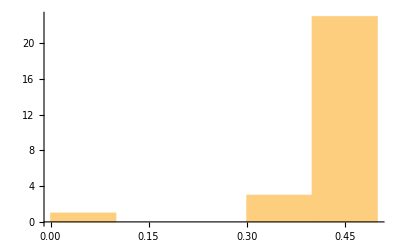
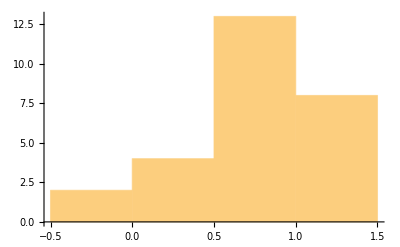
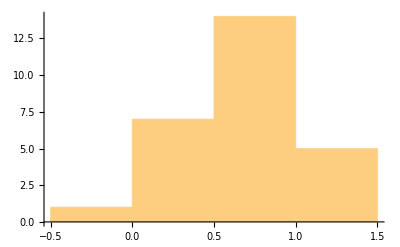
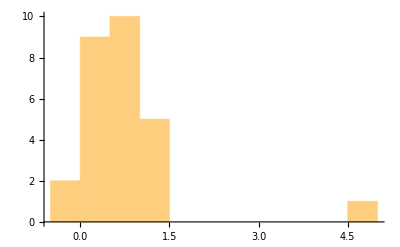
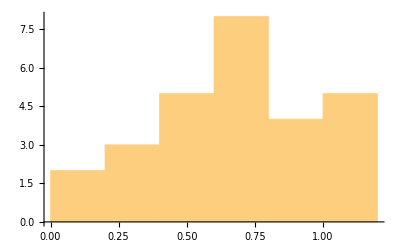
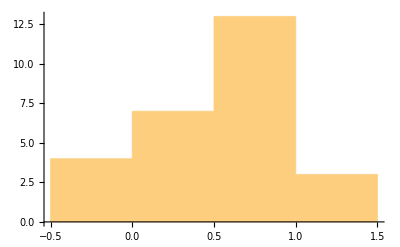
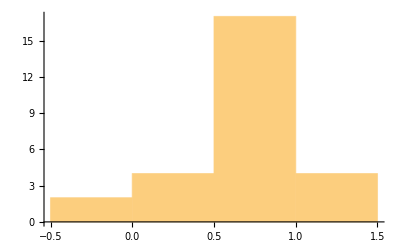
P_α→-Graphics-
P_(1,α)→-Graphics- | P_(1,β)→-Graphics-
P_(2,α)→-Graphics- | P_(2,β)→-Graphics-
P_(3,α)→-Graphics- | P_(3,β)→-Graphics-

```mathematica
(* Let's dig down to a list of the failed algebraic evaluations *)failedRealBoundsEvaluations//Last/@#&//First/@#&//
(* We select the low prevalence solution, it happens to be
the true one, but that is irrelevant now - we are just picking
one consistently. *)
Map[
Select[#,Last@First@#<1/2&]&,
#]& //
(* Flattening everything and collecting under the unknown classifier
accuracies *)
Flatten//GroupBy[#,First]&//Map[Last,#,{2}]&//
(* Making default histograms of the estimates *)
Histogram/@#&//KeySort//
(* Start shaping into a form suitable for Grid *)
Normal//{First@#,Rest@#//Partition[#,2]&}&//
Column[{First@#,First@Rest@#//Grid},Alignment->Center]&
```

## We are not done!

Now we have to formalize our search so we keep track of the feature partition that produced a failure. The search above was a quick one just to see if we could find good and bad candidates for the trios as defined by the algebraic evaluator failure.
So we will do our search in two steps:
1. Randomly train/split as well as feature split. Remember the feature split and the algebraic evaluation.
2. Identify the ones that returned sensible evaluation values and stress test them more. For each feature partition that survived, test it on 10 random train test partitions.

```mathematica
(* Re-doing our initial, quick feature partition search but now remembering
the partition not just the algebraic evaluation *)
classifierTypes = Table["NaiveBayes",{3}];
Timing[runs =Table[

(* The random train/test split *)
runTrainTestSplit=Association[
0->({Take[globalTrainTestSplit[0]//First//RandomSample,6000],Take[globalTrainTestSplit[0]//Last//RandomSample,200]}),
1->({Take[globalTrainTestSplit[1]//First//RandomSample,6000],Take[globalTrainTestSplit[1]//Last//RandomSample,400]})];

(* A random disjoint partition of the dataset features *)
classifiersFeatures=uciAdultFeatures//RandomSample//Partition[#,UpTo@3]&//Take[#,3]&;

(* Training and evaluatin the trio of classifiers *)
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
trainingIndices=Transpose@{
(* Random selection of 0 label training data between the three classifiers *)
RandomSample[Range@6000]//Partition[#,2000]&,
(* Same random selection for the 1 label *)
RandomSample[Range@6000]//Partition[#,2000]&};
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
{classifiersFeatures,AlgebraicallyEvaluateClassifiers[classifiers, classifiersData]},
{100}];]
```

{210.504,Null}

```mathematica
(* Let's identify the survivors of our initial search *)
seeminglyIndependentIndices= MapIndexed[{#2[[1]],#1}&,runs]//
(* Let's select only the evaluations that did not contain imaginary
estimates *)
Select[#,
Not@IsEvaluatorFailureImaginaryQ@First@Last@Last@Last@#&]&//
(* And now the ones with sensible real bounds *)
Select[#,
Not@IsEvaluatorFailureOutOfBoundsRealQ@First@Last@Last@Last@#&]&//First/@#&
```

{1,3,4,9,11,12,14,15,17,18,19,24,26,30,33,34,35,36,37,38,39,40,41,46,47,48,49,50,52,54,55,56,57,58,63,64,66,68,69,70,71,72,74,75,78,79,81,83,84,85,86,87,88,89,90,91,93,96,98,99,100}

```mathematica
Length@seeminglyIndependentIndices
```

61

Okay, so we winnowed out 42 feature partitions. Let’s do this again keeping the winners of the 1st round but running, say, 10 random train/splits on each surviving feature partition.

```mathematica
Clear[DetectFailedEvaluatorRuns]
DetectFailedEvaluatorRuns[runs_]:=Last/@runs//Flatten//Normal//Last/@#&//
((Head/@#//Counts//Keys//MatchQ[#,{Real}]&) && (Min@#>0)&&(Max@#<1))&
Clear[DetectFailedEvaluatorSols]
DetectFailedEvaluatorSols[sols_]:=Last@sols//Flatten//Normal//Last/@#&//
((Head/@#//Counts//Keys//MatchQ[#,{Real}]&) && (Min@#>0)&&(Max@#<1))&
```

```mathematica
classifierTypes
```

{NaiveBayes,NaiveBayes,NaiveBayes}

```mathematica
runs//First/@#&
```

{{{{4,Nominal},{10,Nominal},{1,Numerical}},{{3,Numerical},{5,Nominal},{11,Numerical}},{{2,Nominal},{7,Nominal},{8,Nominal}}},{{{4,Nominal},{3,Numerical},{12,Numerical}},{{9,Nominal},{8,Nominal},{13,Numerical}},{{5,Nominal},{1,Numerical},{2,Nominal}}},{{{9,Nominal},{14,Nominal},{2,Nominal}},{{10,Nominal},{4,Nominal},{13,Numerical}},{{12,Numerical},{8,Nominal},{6,Nominal}}},{{{7,Nominal},{13,Numerical},{10,Nominal}},{{14,Nominal},{6,Nominal},{11,Numerical}},{{2,Nominal},{1,Numerical},{8,Nominal}}},{{{4,Nominal},{2,Nominal},{14,Nominal}},{{5,Nominal},{7,Nominal},{1,Numerical}},{{9,Nominal},{3,Numerical},{8,Nominal}}},{{{1,Numerical},{6,Nominal},{13,Numerical}},{{7,Nominal},{5,Nominal},{8,Nominal}},{{9,Nominal},{11,Numerical},{3,Numerical}}},{{{14,Nominal},{10,Nominal},{6,Nominal}},{{3,Numerical},{11,Numerical},{2,Nominal}},{{12,Numerical},{7,Nominal},{9,Nominal}}},{{{7,Nominal},{11,Numerical},{3,Numerical}},{{4,Nominal},{6,Nominal},{14,Nominal}},{{2,Nominal},{8,Nominal},{5,Nominal}}},{{{11,Numerical},{5,Nominal},{12,Numerical}},{{13,Numerical},{4,Nominal},{10,Nominal}},{{2,Nominal},{7,Nominal},{6,Nominal}}},{{{7,Nominal},{4,Nominal},{12,Numerical}},{{2,Nominal},{13,Numerical},{6,Nominal}},{{8,Nominal},{14,Nominal},{10,Nominal}}},{{{7,Nominal},{10,Nominal},{12,Numerical}},{{4,Nominal},{11,Numerical},{14,Nominal}},{{1,Numerical},{6,Nominal},{8,Nominal}}},{{{7,Nominal},{13,Numerical},{8,Nominal}},{{4,Nominal},{5,Nominal},{14,Nominal}},{{9,Nominal},{3,Numerical},{2,Nominal}}},{{{4,Nominal},{12,Numerical},{6,Nominal}},{{9,Nominal},{2,Nominal},{13,Numerical}},{{8,Nominal},{3,Numerical},{10,Nominal}}},{{{9,Nominal},{1,Numerical},{14,Nominal}},{{3,Numerical},{5,Nominal},{4,Nominal}},{{6,Nominal},{11,Numerical},{10,Nominal}}},{{{5,Nominal},{2,Nominal},{11,Numerical}},{{6,Nominal},{12,Numerical},{1,Numerical}},{{3,Numerical},{13,Numerical},{4,Nominal}}},{{{11,Numerical},{7,Nominal},{10,Nominal}},{{5,Nominal},{6,Nominal},{9,Nominal}},{{8,Nominal},{4,Nominal},{12,Numerical}}},{{{4,Nominal},{2,Nominal},{11,Numerical}},{{7,Nominal},{3,Numerical},{10,Nominal}},{{14,Nominal},{1,Numerical},{9,Nominal}}},{{{9,Nominal},{2,Nominal},{3,Numerical}},{{6,Nominal},{11,Numerical},{5,Nominal}},{{13,Numerical},{14,Nominal},{10,Nominal}}},{{{13,Numerical},{2,Nominal},{9,Nominal}},{{5,Nominal},{10,Nominal},{1,Numerical}},{{7,Nominal},{8,Nominal},{12,Numerical}}},{{{6,Nominal},{14,Nominal},{9,Nominal}},{{1,Numerical},{8,Nominal},{10,Nominal}},{{3,Numerical},{5,Nominal},{2,Nominal}}},{{{2,Nominal},{14,Nominal},{13,Numerical}},{{6,Nominal},{9,Nominal},{3,Numerical}},{{1,Numerical},{8,Nominal},{11,Numerical}}},{{{4,Nominal},{6,Nominal},{2,Nominal}},{{3,Numerical},{14,Nominal},{7,Nominal}},{{10,Nominal},{13,Numerical},{8,Nominal}}},{{{5,Nominal},{14,Nominal},{10,Nominal}},{{6,Nominal},{12,Numerical},{7,Nominal}},{{1,Numerical},{3,Numerical},{11,Numerical}}},{{{13,Numerical},{2,Nominal},{12,Numerical}},{{9,Nominal},{8,Nominal},{11,Numerical}},{{7,Nominal},{10,Nominal},{3,Numerical}}},{{{4,Nominal},{5,Nominal},{13,Numerical}},{{10,Nominal},{12,Numerical},{9,Nominal}},{{6,Nominal},{14,Nominal},{7,Nominal}}},{{{12,Numerical},{11,Numerical},{10,Nominal}},{{6,Nominal},{1,Numerical},{13,Numerical}},{{4,Nominal},{3,Numerical},{8,Nominal}}},{{{4,Nominal},{13,Numerical},{5,Nominal}},{{6,Nominal},{8,Nominal},{14,Nominal}},{{11,Numerical},{2,Nominal},{3,Numerical}}},{{{9,Nominal},{6,Nominal},{11,Numerical}},{{12,Numerical},{1,Numerical},{8,Nominal}},{{13,Numerical},{4,Nominal},{3,Numerical}}},{{{11,Numerical},{5,Nominal},{7,Nominal}},{{2,Nominal},{8,Nominal},{12,Numerical}},{{9,Nominal},{1,Numerical},{6,Nominal}}},{{{7,Nominal},{5,Nominal},{11,Numerical}},{{9,Nominal},{2,Nominal},{1,Numerical}},{{13,Numerical},{12,Numerical},{4,Nominal}}},{{{1,Numerical},{8,Nominal},{12,Numerical}},{{3,Numerical},{9,Nominal},{5,Nominal}},{{7,Nominal},{11,Numerical},{6,Nominal}}},{{{6,Nominal},{14,Nominal},{13,Numerical}},{{2,Nominal},{3,Numerical},{12,Numerical}},{{8,Nominal},{4,Nominal},{10,Nominal}}},{{{3,Numerical},{2,Nominal},{14,Nominal}},{{13,Numerical},{7,Nominal},{1,Numerical}},{{6,Nominal},{11,Numerical},{12,Numerical}}},{{{10,Nominal},{14,Nominal},{4,Nominal}},{{12,Numerical},{9,Nominal},{7,Nominal}},{{2,Nominal},{5,Nominal},{6,Nominal}}},{{{14,Nominal},{7,Nominal},{8,Nominal}},{{5,Nominal},{3,Numerical},{1,Numerical}},{{4,Nominal},{10,Nominal},{13,Numerical}}},{{{7,Nominal},{14,Nominal},{1,Numerical}},{{13,Numerical},{8,Nominal},{4,Nominal}},{{5,Nominal},{12,Numerical},{9,Nominal}}},{{{6,Nominal},{4,Nominal},{12,Numerical}},{{11,Numerical},{13,Numerical},{1,Numerical}},{{10,Nominal},{9,Nominal},{5,Nominal}}},{{{11,Numerical},{1,Numerical},{10,Nominal}},{{6,Nominal},{14,Nominal},{8,Nominal}},{{9,Nominal},{4,Nominal},{2,Nominal}}},{{{9,Nominal},{10,Nominal},{12,Numerical}},{{3,Numerical},{6,Nominal},{5,Nominal}},{{7,Nominal},{11,Numerical},{1,Numerical}}},{{{2,Nominal},{1,Numerical},{9,Nominal}},{{5,Nominal},{6,Nominal},{4,Nominal}},{{7,Nominal},{13,Numerical},{3,Numerical}}},{{{12,Numerical},{13,Numerical},{3,Numerical}},{{8,Nominal},{11,Numerical},{14,Nominal}},{{9,Nominal},{7,Nominal},{4,Nominal}}},{{{9,Nominal},{12,Numerical},{2,Nominal}},{{4,Nominal},{8,Nominal},{5,Nominal}},{{11,Numerical},{3,Numerical},{14,Nominal}}},{{{11,Numerical},{8,Nominal},{3,Numerical}},{{4,Nominal},{9,Nominal},{10,Nominal}},{{1,Numerical},{6,Nominal},{2,Nominal}}},{{{14,Nominal},{8,Nominal},{11,Numerical}},{{4,Nominal},{12,Numerical},{3,Numerical}},{{9,Nominal},{6,Nominal},{1,Numerical}}},{{{2,Nominal},{13,Numerical},{8,Nominal}},{{5,Nominal},{14,Nominal},{11,Numerical}},{{9,Nominal},{3,Numerical},{6,Nominal}}},{{{12,Numerical},{2,Nominal},{5,Nominal}},{{8,Nominal},{6,Nominal},{13,Numerical}},{{14,Nominal},{11,Numerical},{9,Nominal}}},{{{3,Numerical},{6,Nominal},{13,Numerical}},{{4,Nominal},{1,Numerical},{9,Nominal}},{{11,Numerical},{14,Nominal},{10,Nominal}}},{{{5,Nominal},{9,Nominal},{6,Nominal}},{{3,Numerical},{12,Numerical},{13,Numerical}},{{1,Numerical},{11,Numerical},{7,Nominal}}},{{{9,Nominal},{2,Nominal},{11,Numerical}},{{4,Nominal},{6,Nominal},{14,Nominal}},{{8,Nominal},{10,Nominal},{3,Numerical}}},{{{7,Nominal},{12,Numerical},{13,Numerical}},{{11,Numerical},{3,Numerical},{5,Nominal}},{{14,Nominal},{9,Nominal},{4,Nominal}}},{{{4,Nominal},{3,Numerical},{9,Nominal}},{{12,Numerical},{5,Nominal},{11,Numerical}},{{6,Nominal},{7,Nominal},{2,Nominal}}},{{{13,Numerical},{14,Nominal},{6,Nominal}},{{12,Numerical},{11,Numerical},{8,Nominal}},{{9,Nominal},{10,Nominal},{3,Numerical}}},{{{7,Nominal},{12,Numerical},{10,Nominal}},{{14,Nominal},{4,Nominal},{3,Numerical}},{{2,Nominal},{8,Nominal},{6,Nominal}}},{{{5,Nominal},{9,Nominal},{2,Nominal}},{{11,Numerical},{14,Nominal},{7,Nominal}},{{4,Nominal},{8,Nominal},{13,Numerical}}},{{{13,Numerical},{12,Numerical},{14,Nominal}},{{8,Nominal},{7,Nominal},{5,Nominal}},{{3,Numerical},{4,Nominal},{11,Numerical}}},{{{8,Nominal},{4,Nominal},{14,Nominal}},{{11,Numerical},{6,Nominal},{1,Numerical}},{{2,Nominal},{13,Numerical},{7,Nominal}}},{{{4,Nominal},{5,Nominal},{3,Numerical}},{{11,Numerical},{6,Nominal},{7,Nominal}},{{10,Nominal},{9,Nominal},{13,Numerical}}},{{{12,Numerical},{5,Nominal},{4,Nominal}},{{3,Numerical},{2,Nominal},{13,Numerical}},{{9,Nominal},{8,Nominal},{11,Numerical}}},{{{6,Nominal},{11,Numerical},{4,Nominal}},{{8,Nominal},{2,Nominal},{14,Nominal}},{{10,Nominal},{5,Nominal},{1,Numerical}}},{{{9,Nominal},{5,Nominal},{14,Nominal}},{{10,Nominal},{7,Nominal},{8,Nominal}},{{11,Numerical},{6,Nominal},{2,Nominal}}},{{{8,Nominal},{14,Nominal},{11,Numerical}},{{6,Nominal},{4,Nominal},{1,Numerical}},{{7,Nominal},{2,Nominal},{3,Numerical}}},{{{9,Nominal},{8,Nominal},{7,Nominal}},{{5,Nominal},{11,Numerical},{3,Numerical}},{{12,Numerical},{14,Nominal},{6,Nominal}}},{{{12,Numerical},{1,Numerical},{3,Numerical}},{{14,Nominal},{8,Nominal},{7,Nominal}},{{5,Nominal},{13,Numerical},{6,Nominal}}},{{{10,Nominal},{5,Nominal},{1,Numerical}},{{14,Nominal},{4,Nominal},{11,Numerical}},{{12,Numerical},{9,Nominal},{13,Numerical}}},{{{13,Numerical},{3,Numerical},{5,Nominal}},{{9,Nominal},{10,Nominal},{8,Nominal}},{{11,Numerical},{12,Numerical},{4,Nominal}}},{{{7,Nominal},{12,Numerical},{13,Numerical}},{{9,Nominal},{8,Nominal},{14,Nominal}},{{5,Nominal},{2,Nominal},{3,Numerical}}},{{{11,Numerical},{6,Nominal},{4,Nominal}},{{14,Nominal},{13,Numerical},{8,Nominal}},{{12,Numerical},{5,Nominal},{3,Numerical}}},{{{14,Nominal},{6,Nominal},{9,Nominal}},{{10,Nominal},{12,Numerical},{11,Numerical}},{{8,Nominal},{2,Nominal},{3,Numerical}}},{{{7,Nominal},{2,Nominal},{3,Numerical}},{{13,Numerical},{4,Nominal},{10,Nominal}},{{5,Nominal},{6,Nominal},{14,Nominal}}},{{{7,Nominal},{11,Numerical},{12,Numerical}},{{9,Nominal},{1,Numerical},{13,Numerical}},{{8,Nominal},{10,Nominal},{4,Nominal}}},{{{11,Numerical},{7,Nominal},{3,Numerical}},{{4,Nominal},{10,Nominal},{2,Nominal}},{{13,Numerical},{1,Numerical},{14,Nominal}}},{{{5,Nominal},{2,Nominal},{1,Numerical}},{{9,Nominal},{7,Nominal},{3,Numerical}},{{8,Nominal},{12,Numerical},{10,Nominal}}},{{{9,Nominal},{1,Numerical},{7,Nominal}},{{5,Nominal},{13,Numerical},{10,Nominal}},{{14,Nominal},{2,Nominal},{3,Numerical}}},{{{4,Nominal},{9,Nominal},{5,Nominal}},{{6,Nominal},{2,Nominal},{3,Numerical}},{{13,Numerical},{12,Numerical},{11,Numerical}}},{{{2,Nominal},{8,Nominal},{7,Nominal}},{{14,Nominal},{13,Numerical},{9,Nominal}},{{5,Nominal},{12,Numerical},{11,Numerical}}},{{{1,Numerical},{6,Nominal},{2,Nominal}},{{12,Numerical},{4,Nominal},{3,Numerical}},{{7,Nominal},{5,Nominal},{11,Numerical}}},{{{12,Numerical},{14,Nominal},{9,Nominal}},{{8,Nominal},{5,Nominal},{13,Numerical}},{{11,Numerical},{6,Nominal},{2,Nominal}}},{{{4,Nominal},{6,Nominal},{1,Numerical}},{{11,Numerical},{10,Nominal},{14,Nominal}},{{9,Nominal},{2,Nominal},{13,Numerical}}},{{{2,Nominal},{12,Numerical},{1,Numerical}},{{4,Nominal},{11,Numerical},{14,Nominal}},{{5,Nominal},{10,Nominal},{3,Numerical}}},{{{3,Numerical},{13,Numerical},{2,Nominal}},{{9,Nominal},{6,Nominal},{10,Nominal}},{{8,Nominal},{11,Numerical},{14,Nominal}}},{{{8,Nominal},{2,Nominal},{12,Numerical}},{{5,Nominal},{10,Nominal},{14,Nominal}},{{1,Numerical},{9,Nominal},{4,Nominal}}},{{{4,Nominal},{6,Nominal},{7,Nominal}},{{1,Numerical},{8,Nominal},{14,Nominal}},{{12,Numerical},{5,Nominal},{11,Numerical}}},{{{5,Nominal},{8,Nominal},{7,Nominal}},{{12,Numerical},{14,Nominal},{11,Numerical}},{{6,Nominal},{13,Numerical},{10,Nominal}}},{{{1,Numerical},{11,Numerical},{12,Numerical}},{{3,Numerical},{8,Nominal},{5,Nominal}},{{10,Nominal},{2,Nominal},{6,Nominal}}},{{{12,Numerical},{2,Nominal},{1,Numerical}},{{5,Nominal},{7,Nominal},{11,Numerical}},{{14,Nominal},{6,Nominal},{10,Nominal}}},{{{12,Numerical},{13,Numerical},{10,Nominal}},{{7,Nominal},{6,Nominal},{4,Nominal}},{{11,Numerical},{9,Nominal},{3,Numerical}}},{{{13,Numerical},{8,Nominal},{1,Numerical}},{{4,Nominal},{5,Nominal},{10,Nominal}},{{3,Numerical},{14,Nominal},{2,Nominal}}},{{{10,Nominal},{1,Numerical},{11,Numerical}},{{5,Nominal},{3,Numerical},{14,Nominal}},{{6,Nominal},{9,Nominal},{12,Numerical}}},{{{11,Numerical},{3,Numerical},{10,Nominal}},{{14,Nominal},{9,Nominal},{1,Numerical}},{{4,Nominal},{12,Numerical},{6,Nominal}}},{{{10,Nominal},{5,Nominal},{4,Nominal}},{{12,Numerical},{3,Numerical},{7,Nominal}},{{2,Nominal},{9,Nominal},{8,Nominal}}},{{{2,Nominal},{8,Nominal},{13,Numerical}},{{6,Nominal},{12,Numerical},{9,Nominal}},{{7,Nominal},{14,Nominal},{1,Numerical}}},{{{8,Nominal},{11,Numerical},{4,Nominal}},{{9,Nominal},{2,Nominal},{12,Numerical}},{{6,Nominal},{13,Numerical},{5,Nominal}}},{{{4,Nominal},{7,Nominal},{6,Nominal}},{{5,Nominal},{8,Nominal},{12,Numerical}},{{14,Nominal},{1,Numerical},{11,Numerical}}},{{{5,Nominal},{3,Numerical},{9,Nominal}},{{7,Nominal},{4,Nominal},{8,Nominal}},{{12,Numerical},{11,Numerical},{6,Nominal}}},{{{1,Numerical},{10,Nominal},{4,Nominal}},{{14,Nominal},{9,Nominal},{8,Nominal}},{{5,Nominal},{6,Nominal},{13,Numerical}}},{{{6,Nominal},{5,Nominal},{9,Nominal}},{{14,Nominal},{4,Nominal},{3,Numerical}},{{1,Numerical},{2,Nominal},{10,Nominal}}},{{{4,Nominal},{7,Nominal},{5,Nominal}},{{14,Nominal},{10,Nominal},{11,Numerical}},{{6,Nominal},{12,Numerical},{9,Nominal}}},{{{10,Nominal},{9,Nominal},{7,Nominal}},{{13,Numerical},{11,Numerical},{5,Nominal}},{{4,Nominal},{8,Nominal},{2,Nominal}}},{{{11,Numerical},{6,Nominal},{9,Nominal}},{{10,Nominal},{3,Numerical},{7,Nominal}},{{13,Numerical},{5,Nominal},{14,Nominal}}},{{{7,Nominal},{5,Nominal},{4,Nominal}},{{12,Numerical},{14,Nominal},{13,Numerical}},{{10,Nominal},{8,Nominal},{6,Nominal}}}}

```mathematica
tests=TestFeaturePartitions[globalTrainTestSplit,classifierTypes,runs[[seeminglyIndependentIndices]]//First/@#&];
```

```mathematica
tests//Length/@#&//Counts//KeySort
```

<|0→19,1→7,2→9,3→2,4→2,5→3,8→2,10→2,12→1,13→1,16→2,17→1,20→10|>

```mathematica
failedPartitions = seeminglyIndependentIndices[[MapIndexed[{#2[[1]],#1}&,tests]//Select[#,Length@Last@#<20&]&//First/@#&]]
passingPartitions = seeminglyIndependentIndices[[MapIndexed[{#2[[1]],#1}&,tests]//Select[#,Length@Last@#==20&]&//First/@#&]]
```

{1,3,4,9,11,12,14,15,17,18,30,33,34,37,38,39,41,46,47,49,50,52,55,56,57,58,63,64,66,68,69,70,71,72,74,75,78,79,81,83,84,85,86,87,88,89,90,91,93,96,100}

{19,24,26,35,36,40,48,54,98,99}

#### Are we actually reducing the error correlation on the accepted partitions?

Let’s now check if this process of successively winnowing out is actually identifying feature partitions that are likely to result in trios of classifiers nearly independent in their error.

```mathematica
(* Let's forget about the algebraic evaluation part and focus on
inspecting the ground truth values for the performance of the classifiers *)
gtMeasurementsFailed=GTFeaturePartitions[globalTrainTestSplit,classifierTypes,runs[[Complement[Range@100,Join[failedPartitions,passingPartitions]]]]//First/@#&];
```

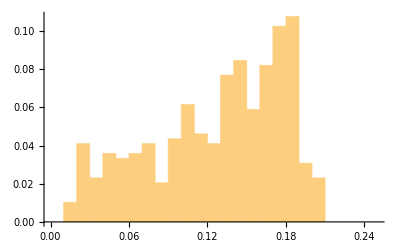

```mathematica
gtMeasurementsFailed//Map[KeySelect[#,MatchQ[#,Subscript[Γ, _,_,_]]&]&,#,{2}]&//Map[Values,#,{2}]&//Map[Abs,#,{3}]&//Map[Max,#,{2}]&//Flatten//Histogram[#,{0.01},"Probability",PlotRange->{{0,0.25},All}]&
```

```mathematica
gtMeasurementsPassed=GTFeaturePartitions[globalTrainTestSplit,classifierTypes,runs[[passingPartitions]]//First/@#&];
```

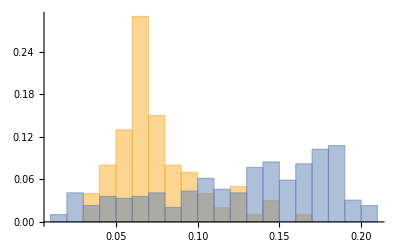

```mathematica
passingValues=gtMeasurementsPassed//Map[KeySelect[#,MatchQ[#,Subscript[Γ, _,_,_]]&]&,#,{2}]&//Map[Values,#,{2}]&//Map[Abs,#,{3}]&//Map[Max,#,{2}]&//Flatten;
failingValues =gtMeasurementsFailed//Map[KeySelect[#,MatchQ[#,Subscript[Γ, _,_,_]]&]&,#,{2}]&//Map[Values,#,{2}]&//Map[Abs,#,{3}]&//Map[Max,#,{2}]&//Flatten;
Histogram[{passingValues, failingValues},{0.01},"Probability",PlotRange->All]
```

Wow! We managed to find trios of classifiers that are less error correlated on unlabeled data. As you
can see, the separation is not clean. The process we have built is, itself, an imperfect detector of
low error correlation. This, itself, seems a paradox. But it isn’t. It is the reality of safety, engineering and invention.
Let’s look at each of these three themes

Necessity is the mother of invention

The algebraic evaluator we have built assuming the classifiers are independent is imperfect. As you saw, small error correlations can lead to estimates that are off from the ground truth values. Yet, having this imperfect tool at hand - the independent algebraic evaluator - we came up with a way to use its failures to create an imperfect filter for classifier trios.

The announcement of the AI Audit Challenge highlighted a pervasive reality of the use of AI currently - most AI systems are black-boxes to its users. This limits our ability to monitor them in detail. Algebraic evaluators can help in those cases by providing the “thermometers” that will alarm or warn about failing or harmful performance.

We see above that using the failures of the independent evaluator allowed us to filter, imperfectly, for nearly independent trios of classifiers. This is, implicitly, an argument about likelihood since the filter is not perfect. Does this mean that we are introducing unstated probability distributions into our approach? Not quite. We have examples in our adoption of older technologies that can help us understand how we can craft this tool to make it useful.

There is nothing new under the sun

Engineering tools to make other tools safe is not new in the history of technology. A history, by the way, that is pre-human. Basic tools that are part of the foundation of much current technology, like fire and the lever, were invented between Homo Habilis and Homo Sapiens. Fire, itself, can serve as rich mine of knowledge and understanding of how the safety of tools is wrapped up in its time, place, and engineering.

Error Correcting (EC) Codes is an example of how we have engineered a nice mathematical idea into a practical tool that works in our phones, laptops and the Voyager probe. The invention of EC codes - algorithms that fix memory errors in computers - is attributed to Hamming. He famously quipped - “Damn It, if the computer knows I made an error, why can’t it fix it?” This lead him to invent Hamming codes. When you pick up any textbook on the theory of EC codes, a couple of points are quickly made:

Any EC code has multiple solutions when decoding. Note the similarity to our algebraic evaluator. It, too, returns multiple solutions when we “decode” the judges decisions into their actual acurracies.

There are many application contexts where we know which of the decoded solutions is correct because we built it that way. In your computer, manufacturing quality means the few bit errors decoding is the correct one. In the Voyager probe, the EC code was engineered to handle the expected noise in space as well as the paramount requirement of low power consumption for transmissions.

Why are there no error-correcting codes for the decisions of noisy judges? Is there a fundamental concept that prevents us from doing this? We don’t think so.

The independent algebraic evaluator is like Hamming's code - a nice proof of concept. But does it work in practice? Can we engineer even something so simple as this independent evaluator to give us some more safety and ability to monitor AI algorithms? There are many ways to take the simple experiment shown here. Does it work on different datasets? Can one extend the math to include the error correlations?

Another well-known example from data analysis can help clarify the allocation of concerns when working with algebraic evaluators. Least squares linear regression is also an algebraic algorithm of the data. It is not a perfect tools but its utility is widely recognized. How well LSLR predicts the ground truth curve for the data is an important concern. But it is one that ultimately depends on the application context of LSLR. The same is true for these algebraic evaluators. The utility of these algebraic formulations will depend on their application context. This now moves to our 3rd theme - what can and cannot be done by algebraic evaluators in the context of AI auditing.

Tools to make other tools safer

The task of AI auditing must be placed in the context of a long history of humankind using tools to keep us safe from earlier tools. That history shows the many factors that go into that societal task. Engineering of a tool is not enough, but is necessary and desired - we should find new tools to make us safer. Algebraic evaluators is such a new tool. It has broad properties that make it useful in the context of AI auditing

They act like thermometers, not a doctors.

Evaluation of noisy classifiers on unlabeled data is like grading a class on a multiple choice exam with two questions. An exam grade is just that. Just a grade. It tells you how you performed on the test. It cannot explain further your conceptual errors or predict what your final class grade will be. But it is useful. It gives you and the teacher a way of understanding where you are in mastering the subject. Algebraic evaluators are simple in the same way thermometers are - measurement devices with no ability to predict or diagnose.

They provide safety in depth.

Doctors work better when they use thermometers to diagnose their patients. We are sure many entries in this challenge will use probability distributions. This is well and good. We need more doctors to audit AI systems, whether those doctors are humans or other machines. Safety in AI systems is increased when we diagnose the problem not just detect its existence. Algebraic evaluators give that added layer of protection that can help these more sophisticated methods for AI auditing. We call them - “thermometers for doctors.”

They are fast and deterministic.

As these computations demonstrate, algebraic evaluation is very fast. No need to carry out multiple MCMC runs, etc. that is common in probability distribution approaches. Getting an answer is quick. This makes it very useful for small, mobile devices.

Their algebraic output signals certifiable failure.

Algebraic evaluators have a “bug” that is a feature. They output algebraic numbers. As such, they can output numbers that are nonsensical as we have been showing here. This is a certifiable failure of their assumptions. We have used that here to explore detectors for violation of the crucial assumption of independence.

They are privacy preserving and compressive in their inputs.

The approach taken here for accuracy evaluation needs 2^n integers for n classifiers. That is 32 integers for 5 classifiers. This is a tiny amount of information. The only thing limiting these integer counters is the samples total size since the 2^n integers must sum to the number of units in the dataset. This small integer size means that it is also privacy preserving. If you are evaluating the performance of X-ray AI diagnosticians, you just need these few integers to evaluate them on a sample. Nobody can reconstruct the original X-rays from these few integers. It is a privacy preserving evaluator.

This important point needs to be noted. What is to prevent a malicious agent from co-opting the AI auditor itself and leaking private information when it has access to the internals of an AI judge? That is a possibility that is not available here. The small number of integer inputs treats the AI judge as a black box and is therefore unable to leak any internal information.

There are many more algebraic evaluators left to build.

The algebraic evaluator discussed here is just one of many possible ones. It only calculates one of many possible statistics of interest. In this way, it is like data streaming algorithms. There is no universal estimator of stream statistics. There is no universal algebraic evaluator. By construction they are meant to estimate a limited set of related statistics - no more, no less.